# Практикум №7. Вектор на плоскости.

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
 14 декабря 2021

## 3. Вектор.

Требуется спроектировать и построить математическую систему, позволяющую решать задачи в области аналитической и компьютерной геометрии. Среда моделирования – символьный математический пакет Mathematica.

### Задание 3.1.

Спроектируйте внутреннее представление объекта «вектор на плоскости».

```mathematica
(*Сначала перенесу из прошлой лабораторной работы все конструкторы, функции для вычисления свойств, построения графического образа объекта точка:*)
ClearAll[kmPoint]
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord]
kmPoint[{ϕ_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[ϕ],ρ Sin[ϕ]}]
kmPoint[id_String,{ϕ_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[ϕ],ρ Sin[ϕ]}]
(*Ниже свойство, которое пришлось подправить в процессе работы.*)
kmPoint[km,id_String,__]["id"]:=id
kmPoint[km,id_String,coord_List,___]["coord"]:=coord;
NamedQ[kmPoint[km,id_String,___]]^:=id!="";
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts]
ClearAll[getLambdaCoords]
getLambdaCoords[pointA_kmPoint,pointB_kmPoint,λ_]:=kmPoint[(pointA["coord"] + λ pointB["coord"])/(λ + 1)]["coord"]
```

```mathematica
(*Представление объекта вектор на плоскости:*)
kmVector[km,"id",{x,y}]
(*{x,y} - координаты вектора в прямоугольной декартовой системе координат.*)
```

kmVector[km,id,{x,y}]

### Задание 3.2.

Постройте булеву функцию NamedQ, позволяющую определить, имеет ли представленный объект «вектор на плоскости» имя.

```mathematica
(*Булева функция для того, чтобы определить, есть ли имя у экземпляра объекта:*)
NamedQ[kmVector[km,id_String,___]]^:=id!="";
(*Проверяю на примерах в следующем задании.*)
```

### Задание 3.3.

Спроектируйте функции-конструкторы объекта «вектор на плоскости».
	Теоретический материал.
	Конструктор называется базовым, если для создания объекта он использует только входные данные, не вызывая другие конструкторы. Это удобно так как при необходимости изменить внутреннее представление объекта, я меняю только базовый конструктор.
	Задать вектор, к примеру, можно, передавая в конструктор:
	1) Декартовы координаты;
	2) Имя и декартовы координаты;
	3) Две различные точки: начало и конец направленного отрезка, соответствующего вектору; 
	4) Имя вектора и две различные точки: начало и конец направленного отрезка, соответствующего вектору;
	5) Орт и длина вектора. 
	6) Имя, орт (единичный вектор, со направленный с задаваемым вектором), и длина вектора;

```mathematica
ClearAll[kmVector]
(*Базовый конструктор для создания объекта по имени и декартовым координатам:*)
(*2)*)
kmVector[id_String,coord_List]:=kmVector[km,id,coord];
(*Остальные, производные конструкторы:*)
(*Конструктор для создания экземпляра объекта по декартовым координатам:*)
(*1)*)
kmVector[coord_List]:=kmVector["",coord];
(*Тестирую:*)
kmVector["hello world",{1,3}]
kmVector["my vector",{10,5}]
kmVector[{1,3}]
kmVector[{2,6}]
```

kmVector[km,hello world,{1,3}]

kmVector[km,my vector,{10,5}]

kmVector[km,,{1,3}]

kmVector[km,,{2,6}]

```mathematica
(*Теперь могу проверить NamedQ:*)
NamedQ[kmVector["AB",{11,-21}]]
NamedQ[kmVector[{0,-7}]]
NamedQ[kmVector["",{-1,1}]]
```

NamedQ[kmVector[km,AB,{11,-21}]]

NamedQ[kmVector[km,,{0,-7}]]

NamedQ[kmVector[km,,{-1,1}]]

### Задание 3.4.

Создайте функции-конструкторы объекта «вектор на плоскости» для случаев, когда вектор задается двумя различными точками: началом и концом направленного отрезка, соответствующего вектору, с указанием имени либо нет. Функции должны сводить вычисления к базовому конструктору 1).

```mathematica
(*По методическому пособию показываю как я пошагово прихожу к созданию конструктора 4):*)
(*Задаю точки A, B и ассоциирую их с символами P0, P1*)
{P0,P1}=MapThread[kmPoint[#1,#2]&,{{"A","B"},{{3,4},{-2,3}}}]
(*Получаю список из двух экземпляров объекта точка с помощью MapThread, которая действует чистой функцией kmPoint[#1,#2]& на выражение {{"A","B"},{{3,4},{-2,3}}*)
```

{kmPoint[km,A,{3,4}],kmPoint[km,B,{-2,3}]}

```mathematica
(*А координаты вектора буду получать с помощью Prefix:*)
P1@"coord"-P0@"coord"
(*Или так:*)
P1["coord"]-P0["coord"]
```

{-5,-1}

{-5,-1}

```mathematica
(*Теперь можно представить окончательный вариант конструктора 4):*)
(*4)*)
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1["coord"]-P0["coord"]]
kmVector["CD",P0,P1]
(*Тестирую:*)
kmVector["a",kmPoint[{1,3}],kmPoint[{7,14}]]
kmVector["b",kmPoint[{10,5}],kmPoint[{6,-12}]]
```

kmVector[km,CD,{-5,-1}]

kmVector[km,a,{6,11}]

kmVector[km,b,{-4,-17}]

```mathematica
(*Конструктор 3) для создания экземпляра объекта по двум различным точкам:*)
(*Так как я не передаю в конструктор имя вектора, я могу его "вычислить", взяв соответствущие имена точек. Или, если имена точек не заданы, "назвать" Вектором:*)
(*Если у точек есть имена, вектор, создаваемый этими точками, именую, подряд записывая имя точки-начала и имя точки-конца направленного отрезка.*)
StringJoin[P0@"id",P1@"id"]
```

AB

```mathematica
(*Как получаю имя? Я использую соединённые с помощью StringJoin имена первой и второй точек.*)
```

```mathematica
(*Чтобы определить, именованы ли точки, использую NamedQ:*)
NamedQ[#]&/@{P0,P1}
And@@NamedQ/@{P0,P1}
(*С помоью Apply заменяю голову списка на And, так как мне важно знать, есть ли имена у обеих точек.*)
```

{True,True}

True

```mathematica
(*А теперь могу получить итоговый вариант конструктора 3):*)
(*3)*)
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"],""],P0,P1];
(*Тестирую:*)
(*Для проверки конструктора пришлось подредактировать оператор, возвращающий свойство id у kmPoint - убрать возврат строки "Точка", если имя не задано.*)
kmVector[kmPoint[{1,3}],kmPoint[{2,4}]]
kmVector[kmPoint["",{3,16}],kmPoint["",{6,11}]]
```

kmVector[km,,{1,1}]

kmVector[km,,{3,-5}]

```mathematica
kmVector[kmPoint["A",{1,4}],kmPoint["B",{5,1}]]
kmVector[kmPoint["Start",{7,2}],kmPoint["End",{1,6}]]
```

kmVector[km,AB,{4,-3}]

kmVector[km,StartEnd,{-6,4}]

### Задание 3.5.

Постройте конструктор объекта «вектор на плоскости» в случае, когда он именован либо нет и задается направлением (вектором-ортом, объектом!) и длиной. Функция должны сводить вычисления к базовому конструктору.

```mathematica
(*Конструктор для создания экземпляра объекта по имени, орту и длине вектора:*)
(*По формуле, для того, чтобы найти орт-вектор необходимо вектор поделить на его длину (или каждую из его координаток). Использую данный факт:*)
(*6)*)
kmVector[id_String,ort_kmVector,vLen_]:=kmVector[id,ort["coord"]*vLen]
kmVector["based on ort",kmVector[{1,1}],5]
```

kmVector[based on ort,5 kmVector[km,,{1,1}][coord]]

```mathematica
(*Конструктор для создания экземпляра орту и длине вектора:*)
(*5)*)
kmVector[ort_kmVector,vLen_]:=kmVector[ort["coord"]*vLen]
kmVector[kmVector[{1,1}],7]
```

kmVector[7 kmVector[km,,{1,1}][coord]]

### Задание 3.6.

Создайте возможность задания объекта «вектор на плоскости» посредством указания имени вектора и его декартовых координат.
	Комментарий: выполнено в задании 3.2.

### Задание 3.7.

Напишите оператор, возвращающий имя объекта «вектор на плоскости», если оно существует, и нарицательное имя “Вектор” в противном случае.

```mathematica
(*Оператор, возвращающий имя объекта на плоскости:*)
kmVector[km,id_String,coord_List]["id"]:=If[id!="",id,"Вектор"]
(*Проверяю:*)
kmVector["vector's name",{1,1}]["id"]
kmVector[{11,39}]["id"]
kmVector["i'm vector",P0,P1]["id"]
kmVector[P0,P1]["id"]
kmVector[kmPoint[{9,1}],kmPoint[{10,4}]]["id"]
```

vector's name

Вектор

i'm vector

AB

Вектор

### Задание 3.8.

Напишите оператор, возвращающий координаты заданного объекта «вектор на плоскости».

```mathematica
kmVector[km,id_String,coord_List]["coord"]:=coord
(*Тестирую:*)
kmVector["hello world",{4,8}]["coord"]
kmVector[{4,4}]["coord"]
kmVector[kmPoint[{0,5}],kmPoint[{1,25}]]["coord"]
kmVector[P0,P1]["coord"]
```

{4,8}

{4,4}

{1,20}

{-5,-1}

### Задание 3.9.

Напишите оператор, возвращающий длину заданного объекта «вектор на плоскости»

```mathematica
(*Построю сначала компьютерную модель для вычисления длины вектора по его заданным координатам:*)
(*Вспоминаю, что:*)
A={Subscript[x, a],Subscript[y, a]}
B={Subscript[x, b],Subscript[y, b]}
```

{x_a,y_a}

{x_b,y_b}

```mathematica
(*Скалярное произведение:*)
A.B
```

x_a x_b+y_a y_b

```mathematica
(*В моём случае мне нужно:*)
A.A
Sqrt[A.A]
```

x_a^2+y_a^2

√(x_a^2+y_a^2)

```mathematica
(*Выходит, что если у вектора V есть координаты {Vx,Vy}, его длину найдём как выражение:*)
Sqrt[{Vx,Vy}.{Vx,Vy}]
```

√(Vx^2+Vy^2)

```mathematica
(*Теперь монжо написать оператор:*)
kmVector[km,id_String,coord_List]["length"]:=Sqrt[coord.coord]
(*Проверяю:*)
kmVector["hello world",{1,8}]["length"]
kmVector[{0,12}]["length"]
kmVector[kmPoint[{10,5}],kmPoint[{9,-4}]]["length"]
kmVector[P0,P1]["length"]
```

√65

12

√82

√26

### Задание 3.10.

Напишите оператор, возвращающий орт заданного объекта «вектор на плоскости»

```mathematica
(*Орт вектора - вектор единичной длины, сонаправленный с вектором V.*)
(*Напишу оператор, используя формулу:*)
kmVector[km,id_String,coord_List]["ort"]:=kmVector[coord/Sqrt[coord.coord]]
(*Проверяю:*)
kmVector[{5,5}]["ort"]
kmVector[{7/Sqrt[2],7/Sqrt[2]}]["ort"]
```

kmVector[km,,{1/(√2),1/(√2)}]

kmVector[km,,{1/(√2),1/(√2)}]

### Задание 3.12.

Постройте в Mathematica выражение, которое определяет, являются ли два вектора, заданные на плоскости, коллинеарными.

```mathematica
(*Построю выражение, проверяющее векторы на коллинеарность. Для этого сначала рассмотрю два вектора:*)
V1=kmVector["a",{ax,ay}]
V2=kmVector["b",{bx,by}]
```

kmVector[km,a,{ax,ay}]

kmVector[km,b,{bx,by}]

```mathematica
(*Так как координаты моих векторов будут элементами матрицы, а мне нужно найти определитель такой матрицы, использую функцию Det:*)
Det[{V1["coord"],V2["coord"]}]
```

-ay bx+ax by

```mathematica
(*Сравнивая с нулём я сразу буду получать однозначный ответ True/False - коллинеарны(=0)/не коллинеарны(!=0).*)
Det[{V1["coord"],V2["coord"]}]===0
```

False

```mathematica
(*Напишу тест-функцию для определения коллинеарности двух векторов:*)
ifVectorsCollinear[V1_kmVector,V2_kmVector]^:=Det[{V1["coord"],V2["coord"]}]===0
(*Проверяю:*)
ifVectorsCollinear[kmVector["hello world",{1,3}],kmVector[{5,8}]]
ifVectorsCollinear[kmVector[{6,4}],kmVector[{3,2}]]
```

False

True

### Задание 3.13.

Постройте булеву функцию isVectorsCollinear, определяющую взаимную направленность двух заданных векторов плоскости. Функция возвращает одно из значений, соответствующих следующему расположению векторов: 1 коллинеарны и сонаправлены, -1 коллинеарны и противонаправлены, 2 не коллинеарны.

```mathematica
isVectorsCollinear[V1_kmVector,V2_kmVector]^:=If[V1["coord"].V2["coord"]>0&&ifVectorsCollinear[V1,V2]===True,1,If[V1["coord"].V2["coord"]<0&&ifVectorsCollinear[V1,V2]===True,-1,2]]
(*Проверяю:*)
isVectorsCollinear[kmVector["hello world",{1,3}],kmVector[{5,8}]]
isVectorsCollinear[kmVector[{6,4}],kmVector[{3,2}]]
isVectorsCollinear[kmVector[{-12,8}],kmVector[{6,-4}]]
```

2

1

-1

### Задание 3.14.

Постройте булеву функцию isVectorsOrthog, определяющую, являются ли два заданных вектора плоскости перпендикулярными.

```mathematica
(*Векторы ортогональны, если их скалярное произведение равно 0:*)
```

```mathematica
isVectorsOrthog[V1_kmVector,V2_kmVector]^:=V1["coord"].V2["coord"]===0
(*Проверяю:*)
isVectorsOrthog[kmVector["hello world",{1,3}],kmVector[{-6,2}]]
isVectorsOrthog[kmVector[{6,4}],kmVector[{3,2}]]
```

True

False

### Задание 3.15.

Постройте функцию VectorsDirection, определяющую взаимное направление двух векторов a и b плоскости. Функция возвращает одно из значений, соответствующих следующему взаимному направлению векторов a и b: 0 перпендикулярны, 1 коллинеарны и со направлены, -1 коллинеарны и противоположно направлены, 2 не коллинеарны и не перпендикулярны.

```mathematica
(*Всё почти так же, как и с функцией isVectorsCollinear:*)
```

```mathematica
VectorsDirection[a_kmVector,b_kmVector]^:=If[isVectorsOrthog[a,b]===True,0,isVectorsCollinear[a,b]]
(*Проверяю:*)
VectorsDirection[kmVector[{1,3}],kmVector[{-6,2}]]
VectorsDirection[kmVector["hello world",{1,3}],kmVector[{5,8}]]
VectorsDirection[kmVector[{6,4}],kmVector[{3,2}]]
VectorsDirection[kmVector[{-12,8}],kmVector[{6,-4}]]
```

0

2

1

-1

### Задание 3.16.

Создайте функцию VectorBisector, вычисляющую единичный вектор, со направленный с биссектрисой угла между векторами a и b.

```mathematica
(*Для начала введу глобальные правила для сложения двух векторов и умножения вектора на константу:*)
(*Сложение:*)
VectsSum[V1_kmVector,V2_kmVector]^:=kmVector[V1["coord"]+V2["coord"]]
VectsSum[V1,V2]
```

kmVector[km,,{ax+bx,ay+by}]

```mathematica
(*Умножения вектора на константу:*)
VectScale[V_kmVector,λ_]^:=kmVector[λ*V["coord"]]
VectScale[V1,k]
```

kmVector[km,,{ax k,ay k}]

```mathematica
V1=kmVector["a",{2,0}]
V2=kmVector["b",{0,5}]
(*Получим векторы одинаковой длины, сонаправленные с заданным:*)
VectScale[V2,V1["length"]]
VectScale[V1,V2["length"]]
```

kmVector[km,a,{2,0}]

kmVector[km,b,{0,5}]

kmVector[km,,{0,10}]

kmVector[km,,{10,0}]

```mathematica
(*Перед сложением записывыаю векторы списком:*)
MapThread[VectScale[#1,#2["length"]]&,{{V1,V2},{V2,V1}}]
```

{kmVector[km,,{10,0}],kmVector[km,,{0,10}]}

```mathematica
VectsSum@@MapThread[VectScale[#1,#2["length"]]&,{{V1,V2},{V2,V1}}]
```

kmVector[km,,{10,10}]

```mathematica
VectorBisector[V1_kmVector,V2_kmVector]^:=VectsSum@@MapThread[VectScale[#1,#2["length"]]&,{{V1,V2},{V2,V1}}]
VectorBisector[kmVector[{6,4}],kmVector[{3,2}]]
```

kmVector[km,,{12 √13,8 √13}]

### Задание 3.17.

Создайте функцию VectorProjection, вычисляющую вектор-проекцию вектора a на вектор b.

```mathematica
V=kmVector["a",{2,0}]
W=kmVector["b",{0,5}]
(*Координаты орта,единичного вектора,со направленного с вектором W*)
W@"ort"
```

kmVector[km,a,{2,0}]

kmVector[km,b,{0,5}]

kmVector[km,,{0,1}]

```mathematica
(W@"ort")@"coord"
```

{0,1}

```mathematica
(*Скалярное произведение векторов V и единичного вектора,со направленного с вектором W:*)
Dot[V@"coord",#]&[(W@"ort")@"coord"]
```

0

```mathematica
VectScale[#,Dot[V@"coord",(#)@"coord"]]&[(W@"ort")]
```

kmVector[km,,{0,0}]

```mathematica
(*Итоговая функция:*)
VectorProjection[V_kmVector,W_kmVector]^:=VectScale[#,Dot[V@"coord",(#)@"coord"]]&[(W@"ort")]
VectorProjection[V,W]
```

kmVector[km,,{0,0}]

### Задание 3.21.

Решите предложенные ниже задачи, используя построенную ранее систему «точка и вектор на плоскости»: 
а) напишите функции пользователя; 
б) в текстовых ячейках запишите спецификации построенных функций; 
в) тестируйте функции на конкретных экземплярах объектов; 
г) изобразите в графической области геометрические объекты, фигурирующие в задаче.

### Задание 3.21.1

Напишите функцию, которая вычисляет длину медианы AD треугольника ABC, если даны координаты его вершин А(xA, yA), B(xB, yB) и C(xC, yC). Использовать понятие вектора.
	Спецификация функции.
	GetMedianAD[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=kmVector[P1,kmPoint["D",(P3["coord"]+P2["coord"])*1/2]]@"length"
	Имя функции:  GetMedianAD.
	Аргументы функции: P1_kmPoint, P2_kmPoint, P3_kmPoint - экземпляры объекта точка на плоскости.
	Назначение функции: вычисляет длину медианы AD в треугольнике ABC. Координаты вершин треугольника известны, они передаются в функцию при вызове. В самой функции я нахожу координаты середины BC, создаю экземпляр объекта вектор на плоскости и вычисляю его длину.

kmPoint[km,A,{-3,-2}]

kmPoint[km,B,{4,5}]

kmPoint[km,C,{8,-5}]

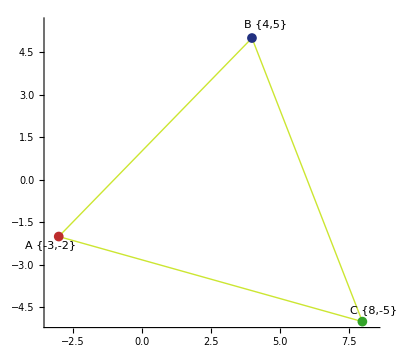

```mathematica
(*Пусть даны вершины, которые я решил задать объектам точка:*)
pointA=kmPoint["A",{-3,-2}]
pointB=kmPoint["B",{4,5}]
pointC=kmPoint["C",{8,-5}]
(*Напишу функцию для графического отображения треугольника по точкам:*)
printTriangle[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=Graphics[{Hue[0.19,0.78,0.9],Line[{P1["coord"],P2["coord"],P3["coord"],P1["coord"]}],AbsolutePointSize[7],Hue[0,0.76,0.74],Point[P1["coord"]],AbsolutePointSize[7],Hue[0.64,0.74,0.5],Point[P2["coord"]],AbsolutePointSize[7],Hue[0.32,0.75,0.64],Point[P3["coord"]],Hue[0.5,0.5,0],Text["A"Text[P1["coord"]],P1["coord"]-0.3],Hue[0.5,0.5,0],Text["B"Text[P2["coord"]],P2["coord"]+0.5],Hue[0.5,0.5,0],Text["C"Text[P3["coord"]],P3["coord"]+0.4]},PlotRange->All,Axes->True]
(*Проверяю:*)
myTriangle=printTriangle[pointA,pointB,pointC]
```

```mathematica
(*Напишу функцию нахождения медианы AD. Так как даны координаты B и C, я могу найти середину BD по координатам*)
(*Получу координаты точки D:*)
(pointC["coord"]+pointB["coord"])*1/2
(*Экземпляр объекта, точка D:*)
pointD=kmPoint["D",(pointC["coord"]+pointB["coord"])*1/2]
(*Вектор AD:*)
vectorAD=kmVector[pointA,pointD]
```

{6,0}

kmPoint[km,D,{6,0}]

kmVector[km,AD,{9,2}]

```mathematica
(*И нахожу длину:*)
vectorAD@"length"
```

√85

```mathematica
(*Теперь можно записать функцию целиком:*)
GetMedianAD[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=kmVector[P1,kmPoint["D",(P3["coord"]+P2["coord"])*1/2]]@"length"
GetMedianAD[pointA,pointB,pointC]
```

√85

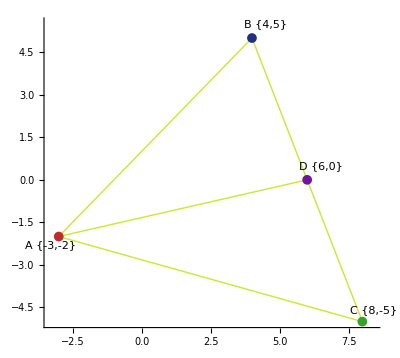

```mathematica
(*Теперь добавлю на график медиану и точку D:*)
myTriangleWithAD=Show[Graphics[{Hue[0.19,0.78,0.9],Line[{pointA["coord"],pointD["coord"]}]},PlotRange->All,Axes->True],myTriangle,Graphics[{AbsolutePointSize[7],Hue[0.78,0.86,0.61],Point[pointD["coord"]],Hue[0.5,0.5,0],Text["D"Text[pointD["coord"]],pointD["coord"]+0.5]}]]
```

### Задание 3.21.2

Напишите функцию, которая вычисляет точку пересечения медиан треугольника ABC, если даны координаты его вершин А(xA, yA), B(xB, yB), C(xC, yC). Использовать понятие вектора.
	Спецификация функции.
	getMedianCenterCoord[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=getLambdaCoords[P2,kmPoint["F",(P3["coord"]+P1["coord"])*1/2],2]
	Имя функции:  getMedianCenterCoord.
	Аргументы функции: P1_kmPoint, P2_kmPoint, P3_kmPoint - экземпляры объекта точка на плоскости.
	Назначение функции: вычисляет координаты точки O - центра пересечения медиан в треугольнике ABC. Координаты вершин треугольника известны, они передаются в функцию при вызове. В самой функции я нахожу координаты точки F середины AC, создаю экземпляр объекта точка на плоскости F. А дальше, зная, что медианы точкой пересечения делятся в отношени 2:1, я использую описанную ранее в ЛР6 функцию getLambdaCoords, возвращающую координаты точки, делящей отрезок заданный координатами своих концов в отношении λ.

```mathematica
(*Пусть даны вершины, которые я решил задать объектам точка:*)
pointA=kmPoint["A",{-3,-2}]
pointB=kmPoint["B",{4,5}]
pointC=kmPoint["C",{8,-5}]
```

kmPoint[km,A,{-3,-2}]

kmPoint[km,B,{4,5}]

kmPoint[km,C,{8,-5}]

```mathematica
(*Предлагаю найти координаты середин сторон AB и AC:*)
(pointB["coord"]+pointA["coord"])*1/2
(pointC["coord"]+pointA["coord"])*1/2
```

{1/2,3/2}

{5/2,-7/2}

```mathematica
(*Назову их и создам соответствующие экземпляры объектов:*)
pointL=kmPoint["L",(pointB["coord"]+pointA["coord"])*1/2]
pointF=kmPoint["F",(pointC["coord"]+pointA["coord"])*1/2]
```

kmPoint[km,L,{1/2,3/2}]

kmPoint[km,F,{5/2,-7/2}]

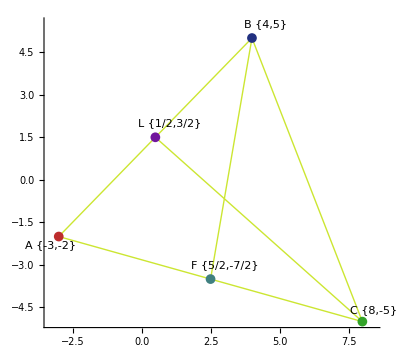

```mathematica
(*Теперь условие задачи удобно отобразить графически:*)
myTriangleWithMedians=Show[Graphics[{Hue[0.19,0.78,0.9],Line[{pointC["coord"],pointL["coord"]}],Line[{pointB["coord"],pointF["coord"]}]},PlotRange->All,Axes->True],myTriangle,Graphics[{AbsolutePointSize[7],Hue[0.78,0.86,0.61],Point[pointL["coord"]],Hue[0.5,0.5,0],Text["L"Text[pointL["coord"]],pointL["coord"]+0.5],Hue[0.5,0.5,0.5],Point[pointF["coord"]],Hue[0.5,0.5,0],Text["F"Text[pointF["coord"]],pointF["coord"]+0.5]}]]
```

```mathematica
(*Из шестой лабораторной работы использую функцию, возвращающую координаты точки, делящей отрезок,заданный координатами своих концов в отношении λ, в моём случае λ - это 2:1.*)
getLambdaCoords[pointB,pointF,2]
```

{3,-2/3}

```mathematica
(*Запишу в виде функции:*)
getMedianCenterCoord[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=getLambdaCoords[P2,kmPoint["F",(P3["coord"]+P1["coord"])*1/2],2]
pointO=getMedianCenterCoord[pointA,pointB,pointC]
```

{3,-2/3}

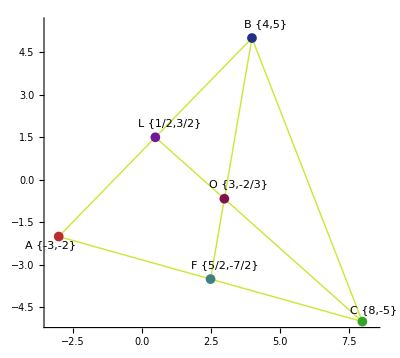

```mathematica
(*Теперь можно отобразить графически ответ:*)
myTriangleWithO=Show[myTriangleWithMedians,Graphics[{AbsolutePointSize[7],Hue[0.91,0.85,0.5],Point[pointO],Hue[0.5,0.5,0],Text["O"Text[pointO],pointO+0.5]}]]
```

### Задание 3.21.3

Заданы вершины А(xA, yA), B(xB, yB) и точка M(xM, yM) пересечения медиан треугольника ABC. Напишите функцию, которая вычисляет координаты вершины C. Использовать понятие вектора.
Спецификация функции.
	getpointCCoord[P1_kmPoint,P2_kmPoint,P0_kmPoint]^:=(P0["coord"](1/2+1)-(P1["coord"]+P2["coord"])*1/2)/(1/2)
	Имя функции:  getpointCCoord.
	Аргументы функции: P1_kmPoint, P2_kmPoint, PO_kmPoint - экземпляры объекта точка на плоскости.
	Назначение функции: вычисляет координаты вершины C по вершинам A, B, и точке пересечения медиан O треугольника ABC. Из формулы нахождения координат точки, делящей отрезок заданный координатами своих концов в отношении λ выражаю один из концов - свою точку C.

```mathematica
(*Пусть даны вершины, которые я решил задать объектам точка:*)
pointA=kmPoint["A",{-3,-2}]
pointB=kmPoint["B",{4,5}]
pointO=kmPoint["O",{3,-2/3}]
```

kmPoint[km,A,{-3,-2}]

kmPoint[km,B,{4,5}]

kmPoint[km,O,{3,-2/3}]

```mathematica
(*График условия задачи неотличим от предыдущей, только точка C является неизвествой.*)
(*Координаты точки C нахожу следующим образом.*)
(*Опять середина AB - точка L:*)
pointL=kmPoint["L",(pointA["coord"]+pointB["coord"])*1/2]
(*Напишу общую формулу для нахождения точки C: обратно для случая нахождения координат точки, делящей отрезок,заданный координатами своих концов в отношении λ:*)
(pointO["coord"](1/2+1)-pointL["coord"])/(1/2)
```

kmPoint[km,L,{1/2,3/2}]

{8,-5}

```mathematica
(*Теперь могу написать функцию:*)
getpointCCoord[P1_kmPoint,P2_kmPoint,P0_kmPoint]^:=(P0["coord"](1/2+1)-(P1["coord"]+P2["coord"])*1/2)/(1/2)
getpointCCoord[pointA,pointB,pointO]
```

{8,-5}

### Задание 3.21.4

Треугольник ABC задан координатами своих вершин А(xA, yA), B(xB, yB), C(xC, yC). Напишите функцию, которая вычисляет расстояние от начала координат до точки пересечения медиан этого треугольника. Использовать понятие вектора.
Спецификация функции.	getLenFromStart[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=kmVector[kmPoint["start",{0,0}],kmPoint["O",getMedianCenter[P1,P2,P3]]]@"length"
	Имя функции:  getLenFromStart.
	Аргументы функции: P1_kmPoint, P2_kmPoint, P3_kmPoint - экземпляры объекта точка на плоскости.
	Назначение функции: вычисляет расстояние от начала координат до точки пересечения медиан этого треугольника O. Нахожу посредством вычисления длины экземпляра объекта вектор заданного координатами точек начала координат и центра пересечения медиан.

```mathematica
(*Пусть даны вершины, которые я решил задать объектам точка:*)
pointA=kmPoint["A",{-3,-2}]
pointB=kmPoint["B",{4,5}]
pointC=kmPoint["C",{8,-5}]
point0=kmPoint["0",{0,0}]
pointO=kmPoint["O",getMedianCenterCoord[pointA,pointB,pointC]]
```

kmPoint[km,A,{-3,-2}]

kmPoint[km,B,{4,5}]

kmPoint[km,C,{8,-5}]

kmPoint[km,0,{0,0}]

kmPoint[km,O,{3,-2/3}]

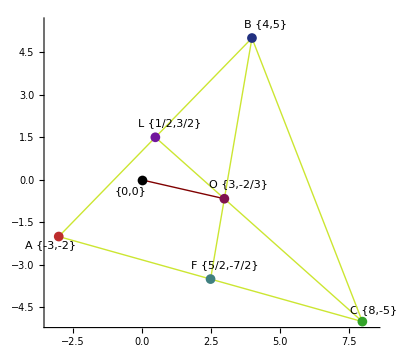

```mathematica
(*Графически условие задачи выглядит следующим образом:*)
Show[Graphics[{Hue[0,0.99,0.5],Line[{point0["coord"],pointO["coord"]}]},PlotRange->All,Axes->True],Graphics[{AbsolutePointSize[7],Point[{0,0}],Text["{0,0}",{0,0}-0.4]}],myTriangleWithO]
```

```mathematica
(*Найду расстояние от начала координат до точки пересечения медиан этого треугольника как длину вектора:*)
kmVector[point0,pointO]@"length"
```

(√85)/3

```mathematica
(*В виде функции:*)
getLenFromStart[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=kmVector[kmPoint["start",{0,0}],kmPoint["O",getMedianCenterCoord[P1,P2,P3]]]@"length"
getLenFromStart[pointA,pointB,pointC]
```

(√85)/3

### Задание 3.21.5

Треугольник ABC задан координатами своих вершин А(xA, yA), B(xB, yB), C(xC, yC). Напишите функцию, которая вычисляет расстояние от вершины А до основания H высоты, опущенной из вершины В на сторону AC. Использовать понятие проекции вектора на вектор.
Спецификация функции.	getAH[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=kmVector[P1,kmPoint["H",VectorProjection[kmVector[P2@"coord"-P1@"coord"],kmVector[P3@"coord"-P1@"coord"]]["coord"]+P1["coord"]]]@"length"
	Имя функции:  getAH.
	Аргументы функции: P1_kmPoint, P2_kmPoint, P3_kmPoint - экземпляры объекта точка на плоскости.
	Назначение функции: вычисляет расстояние от вершины А до основания H высоты, опущенной из вершины В на сторону AC. Нахожу посредством вычисления длины экземпляра объекта вектор AH, заданного объектами точка A и точка H. Координаты последней получаю, выражая через координаты вектора-проекции AB на AC и точки A.

```mathematica
(*Пусть даны вершины, которые я решил задать объектам точка:*) 
pointA=kmPoint["A",{-3,-2}]
pointB=kmPoint["B",{4,5}]
pointC=kmPoint["C",{8,-5}]
pointH=kmPoint["H",{x,y}]
```

kmPoint[km,A,{-3,-2}]

kmPoint[km,B,{4,5}]

kmPoint[km,C,{8,-5}]

kmPoint[km,H,{x,y}]

```mathematica
(*Проекция ветора AB на вектор AC будет иметь вид:*)
vectorAB=kmVector[pointB@"coord"-pointA@"coord"]
vectorAC=kmVector[pointC@"coord"-pointA@"coord"]
VectorProjection[vectorAB,vectorAC]
```

kmVector[km,,{7,7}]

kmVector[km,,{11,-3}]

kmVector[km,,{308/65,-84/65}]

```mathematica
(*А её длина:*)
VectorProjection[vectorAB,vectorAC]["length"]
```

28 √(2/65)

```mathematica
(*Определю координаты точки перечения высоты и стороны AC:*)
kmVector["pr",pointH["coord"]-pointA["coord"]]["coord"]==VectorProjection[vectorAB,vectorAC]["coord"]
```

{3+x,2+y}=={308/65,-84/65}

```mathematica
(*Получается, что мне нужно:*)
pointH=kmPoint["H",VectorProjection[vectorAB,vectorAC]["coord"]+pointA["coord"]]
```

kmPoint[km,H,{113/65,-214/65}]

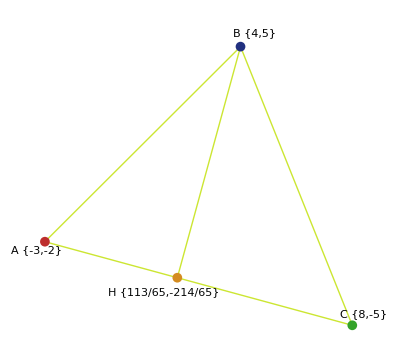

```mathematica
(*Теперь высоту удобно показать графически:*)
Show[Graphics[{Hue[0.19,0.78,0.9],Line[{pointB["coord"],pointH["coord"]}]}],myTriangle,Graphics[{AbsolutePointSize[7],Hue[0.1,0.85,0.83],Point[pointH["coord"]],Hue[0.5,0.5,0.02],Text["H"Text[pointH["coord"]],pointH["coord"]-0.5]}]]
```

```mathematica
(*Задам вектор AH:*)
vectorAH=kmVector[pointA,pointH]
```

kmVector[km,AH,{308/65,-84/65}]

```mathematica
(*Нахожу его длину:*)
vectorAH@"length"
```

28 √(2/65)

```mathematica
(*Теперь попробую все выражения запихнуть в функцию:*)
getAH[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=kmVector[P1,kmPoint["H",VectorProjection[kmVector[P2@"coord"-P1@"coord"],kmVector[P3@"coord"-P1@"coord"]]["coord"]+P1["coord"]]]@"length"
getAH[pointA,pointB,pointC]
```

28 √(2/65)

### Задание 3.21.6

Заданы три последовательных вершины параллелограмма ABCD координатами А(xA, yA), B(xB, yB), C(xC, yC). Напишите функцию, которая вычисляет координаты четвертой вершины D.
	Спецификация функции.	getDPointOfParallelogram[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=Block[{P4=kmPoint["D",{x,y}]},kmVector[P1,P4]["coord"]=kmVector[P2,P3]["coord"]]
getDPointOfParallelogram[pointA,pointB,pointC]
	Имя функции:  getDPointOfParallelogram.
	Аргументы функции: P1_kmPoint, P2_kmPoint, P3_kmPoint - экземпляры объекта точка на плоскости.
	Назначение функции: вычисляет координаты четвертой вершины D. Нахожу посредством вычисления длины экземпляра объекта вектор BC, заданного объектами точка B и точка C. Так как A{0,0}, могу приравнять координаты двух векторов.

```mathematica
(*Пусть даны вершины, которые я решил задать объектам точка на плоскости:*)
pointA=kmPoint["A",{0,0}]
pointB=kmPoint["B",{5,0}]
pointC=kmPoint["C",{12,-3}]
pointD=kmPoint["D",{x,y}]
```

kmPoint[km,A,{0,0}]

kmPoint[km,B,{5,0}]

kmPoint[km,C,{12,-3}]

kmPoint[km,D,{x,y}]

```mathematica
(*Предлагаю найти вектор BC:*)
vectorBC=kmVector[pointB,pointC]
```

kmVector[km,BC,{7,-3}]

```mathematica
(*Мы знаем, что векторы BC и AD равны: они сонаправлены и одинаковы. Вектор AD будет иметь вид:*)
vectorAD=kmVector[pointA,pointD]
```

kmVector[km,AD,{x,y}]

```mathematica
(*Остаётся приравнять векторы, найдя x, y:*)
vectorBC["coord"]
vectorAD["coord"]
```

{7,-3}

{x,y}

```mathematica
vectorAD["coord"]=vectorBC["coord"]
```

{7,-3}

```mathematica
(*Напишу теперь функцию:*)
getDPointOfParallelogram[P1_kmPoint,P2_kmPoint,P3_kmPoint]^:=Block[{P4=kmPoint["D",{x,y}]},kmVector[P1,P4]["coord"]=kmVector[P2,P3]["coord"]]
getDPointOfParallelogram[pointA,pointB,pointC]
```

{7,-3}

kmPoint[km,D,{7,-3}]

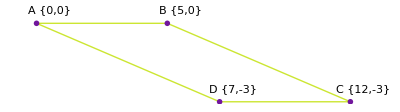

```mathematica
(*Осталось изобразить графически результат:*)
pointD=kmPoint["D",getDPointOfParallelogram[pointA,pointB,pointC]]
Show[Graphics[{Hue[0.19,0.78,0.9],Line[{pointA["coord"],pointB["coord"],pointC["coord"],pointD["coord"],pointA["coord"]}]}],Graphics[{AbsolutePointSize[4],Hue[0.78,0.86,0.61],Point[pointA["coord"]],Hue[0.5,0.5,0],Text["A"Text[pointA["coord"]],pointA["coord"]+0.5]}],Graphics[{AbsolutePointSize[4],Hue[0.78,0.86,0.61],Point[pointB["coord"]],Hue[0.5,0.5,0],Text["B"Text[pointB["coord"]],pointB["coord"]+0.5]}],
Graphics[{AbsolutePointSize[4],Hue[0.78,0.86,0.61],Point[pointC["coord"]],Hue[0.5,0.5,0],Text["C"Text[pointC["coord"]],pointC["coord"]+0.5]}],Graphics[{AbsolutePointSize[4],Hue[0.78,0.86,0.61],Point[pointD["coord"]],Hue[0.5,0.5,0],Text["D"Text[pointD["coord"]],pointD["coord"]+0.5]}]]
```